===============================================================================

Dalam menjawab soal-soal berikut, saya mengasumsikan bahwa orang awam adalah orang - orang dengan kemampuan matematika yang cukup serta berkeinginan untuk mempelajari atau menerapkan Wolfram Mathematica.

===============================================================================
===============================================================================

1.
Diketahui sebuah fungsi r=2-2sin(θ) + (sin(θ)√(|cos(θ)|))/(sin(θ)+1.4)
Gambarkan fungsi tersebut di koordinat polar dan cari luasnya dengan integral monte carlo 10000 titik
Hint: Diketahui luas eksaknya adalah 12.523

------------------------------------------------------------------------------------------------------------------------------------------

Untuk mendapatkan ide apa yang akan kita kerjakan, mari kita buat Plot dari fungsi tersebut

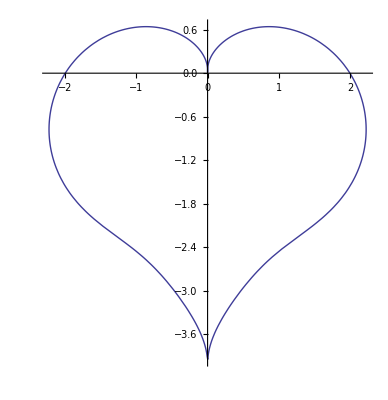

```mathematica
PolarPlot[
2-2Sin[θ]+(Sin[θ] √Abs[Cos[θ]])/(Sin[θ]+1.4),{θ,0,2π}
]
```

Fungsi tersebut memiliki:
- x_min sekitar -2.4
- x_max sekitar 2.4
- y_min=-4
- y_max sekitar 0.7

Maka kita akan dasarkan fungsi yang akan dibuat dengan membuat persebaran titik di X pada [-2.4,2.4] dan persebaran titik di Y pada [-4,0.7]

Sebelum kita mendefinisikan fungsi tersebut, kita perlu mengidentifikasi parameter-parameter yang perlu digunakan.
Paramater-parameter tersebut yaitu:
1. RandomX (memetakan titik-titik acak di X) 	-> RndX
2. RandomY (memetakan titik-titik acak di Y) 	-> RndY
3. Plot 						-> plt, ListTitik
4. Titik yang berada dalam area yang diarsir 	-> Titik
5. Luas Approksimasi				-> LuasAppr
6. Luas Eksak atau Luas Sebenarnya 		-> LuasAsli
7. Galat metode Monte Carlo 			-> Galat
Ketujuh parameter ini akan masuk dalam fungsi yang didefinisikan.

Sekarang, kita definisikan sebuah fungsi bernama MonteCarlo di mana MonteCarlo akan menerima input n dimana n adalah jumlah titik yang disebar.

```mathematica
MonteCarlo[n_]:=
Module[
{RndX,RndY,plt,ListTitik,Titik,LuasAppr,LuasAsli,Galat},

RndX = Table[RandomReal[{-2.4,2.4}],{x,1,n}];
RndY = Table[RandomReal[{-4,0.7}],{x,1,n}];

plt=PolarPlot[
2-2Sin[θ]+(Sin[θ] √Abs[Cos[θ]])/(Sin[θ]+1.4),{θ,0,2π},
Frame->True,
Background->RGBColor[44/255,176/255,55/255],
PlotStyle->{Red,Thickness[0.01]},
PlotLegends->SwatchLegend["Expressions",
LegendFunction->(Framed[#,Background->Gray]&)]
];

ListTitik=ListPlot[
Table[
{RndX[[i]],RndY[[i]]},{i,n}
],
Background->RGBColor[44/255,176/255,55/255]
];

Titik=0;
For[
i=1,i≤n,i++,
If[
N[ArcTan[RndY[[i]]]]≤ 2-2Sin[N[ArcTan[1/RndX[[i]]]]]+(Sin[N[ArcTan[1/RndX[[i]]]]] √Abs[Cos[N[ArcTan[1/RndX[[i]]]]]])/(Sin[N[ArcTan[1/RndX[[i]]]]]+1.4),
Titik=Titik+1
]
];

LuasAppr=N[Titik/n*4.8*(2-2Sin[N[ArcTan[-2.4]]]+(Sin[N[ArcTan[-2.4]]] √Abs[Cos[N[ArcTan[-2.4]]]])/(Sin[N[ArcTan[-2.4]]]+1.4))];

LuasAsli=12.523;

Galat=Abs[LuasAsli-LuasAppr];

Print[
"Luas fungsi menggunakan metode Monte Carlo: ", LuasAppr, " satuan luas"
];
Print[
"Luas fungsi sebenarnya: ", LuasAsli, " satuan luas"
];
Print[
"
Galat metode Monte Carlo: ", Galat, " satuan luas"
];

Show[
plt, ListTitik
]
]
```

Sekarang kita masukkan input n tersebut yaitu 10000

Luas fungsi menggunakan metode Monte Carlo: 12.5717 satuan luas

Luas fungsi sebenarnya: 12.523 satuan luas

Galat metode Monte Carlo: 0.0486557 satuan luas

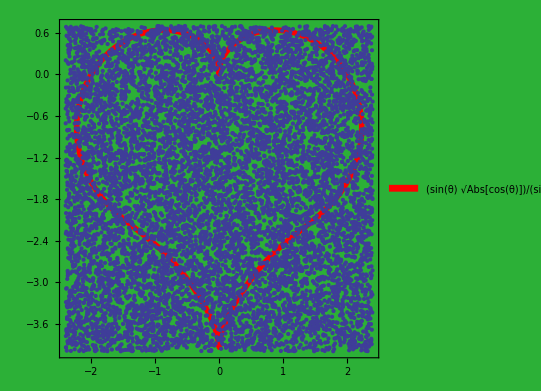

```mathematica
MonteCarlo[10000]
```

Dengan ini, soal nomor 1 telah terjawab.

===============================================================================
===============================================================================

2.1.
Apakah barisan a_n=(2n)^(1/n) konvergen?
Jika iya, maka dia konvergen ke mana?
Jelaskan jawabanmu

------------------------------------------------------------------------------------------------------------------------------------------

Pertama-tama, mari kita definisikan a_n

```mathematica
a[n_]:=(2n)^(1/n)
```

Untuk melihat apakah a_n konvergen atau tidak, kita dapat gunakan ListPlot untuk menggambarkan persebaran fungsi tersebut

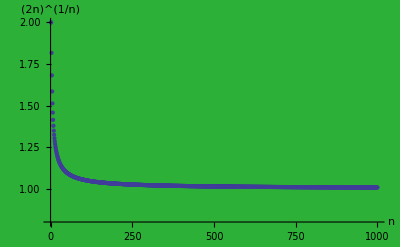

```mathematica
ListPlot[
Table[
a[n],{n,1,1000}
],
PlotRange->{0.8,2},
AxesLabel->{"n","(2n)^(1/n)"},
Background->RGBColor[44/255,176/255,55/255]
]
```

Di sini, terlihat bahwa semakin besar nilai n, maka (2n)^(1/n) akan semakin menuju 1.

Kita dapat gunakan Limit untuk memastikan hal tersebut.

```mathematica
Limit[(2n)^(1/n),n->∞]
```

1

Maka, (2n)^(1/n) konvergen ke 1.

Dengan ini, soal nomor 2 telah terjawab.

===============================================================================
===============================================================================

3.
Buatlah program untuk menghitung nilai faktorial

------------------------------------------------------------------------------------------------------------------------------------------

Faktorial didefinisikan sebagai: n! = n *(n - 1) * (n-2) * ...* 3 * 2 * 1

Untuk membuat fungsinya, kita perlu mengidentifikasi parameter yang akan ada di dalam fungsi ini:
1. Sebuah variable untuk melakukan iterasi
	Variable ini kita namakan i di mana kita akan memulai dengan i=n dan i akan berkurang 1 setiap iterasi
	
2. Sebuah wadah untuk hasil perkalian
	Wadah ini kita namakan Fact di mana kita buat Fact=1
	sehingga saat dikalikan dengan sebuah skalar sembarang k:	Fact =k
	dan pada iterasi berikutnya saat dikalikan dengan (k-1): 	Fact =k * (k - 1)
	hingga pada iterasi terakhir:						Fact =k!

```mathematica
Fact[n_]:=
Module[
{i, Fact},

Fact = 1;
i = n;
While[
i>1,
Fact = Fact * i;
i = i - 1
];

Return[
Fact
]
]
```

Dengan ini kita telah membuat fungsi yang menghitung nilai faktorial sesuai angka yang diinput.

Mari kita coba dengan misalkan n=5 dan n=8

```mathematica
Fact[5]
```

120

5! = 5 * 4 * 3 * 2 * 1=120, maka telah sesuai

```mathematica
Fact[8]
```

40320

8! = 8 * 7 * 6 * 5! = 40320, maka telah sesuai

Dengan ini, soal nomor 3 telah terjawab.

===============================================================================
===============================================================================